4

{{3.,0.,0.},{0.,5.,0.},{0.,0.,1.}}

(3. | 0. | 0.
0. | 5. | 0.
0. | 0. | 1.)

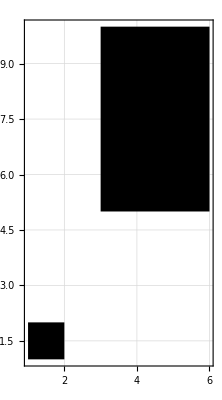

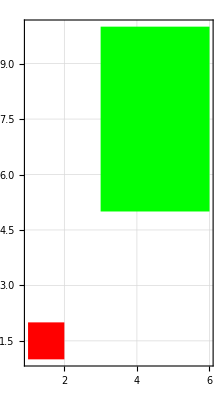

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

```mathematica
question =4
xpp = {
{{2,2},{3,2},{3,3},{2,3}}, 
 {{0, Sqrt[2]},{Sqrt[2] - (1/Sqrt[2]), Sqrt[2] + (1/Sqrt[2])},{0, 2*Sqrt[2]},{(1/Sqrt[2])- Sqrt[2],(1/Sqrt[2])+ Sqrt[2]}},
 {{-1,1},{-1,2},{-2,2}, {-2,1}},
{{3,5},{6,5},{6,10}, {3,10}},
{{4,6},{5,11},{8,12}, {7,7}},
{{0,2},{0,3},{-1, 3}, {-1,2}},
{{-2,2},{-2,3},{-3,3},{-3,2}},
{{4,6},{7,6},{7,11},{4,11}},
{{-5,3},{-5,6},{-10,6},{-10,3}},
{{-6,4},{-11,5},{-12,8},{-7,7}}
};
x = {{1,1},{2,1},{2,2},{1,2}};
xp = xpp[[question]];
MatrixForm[x];
MatrixForm[xp];
{error, f} = FindGeometricTransform[xp, x];
m = Round[TransformationMatrix[f],0.01]
MatrixForm[m]
g = Polygon[x,VertexColors->{Red,Green,Blue, Yellow}];
Graphics[{g,GeometricTransformation[g,f]}, GridLines->Automatic, Frame->True]
Graphics[{{Red,Polygon[x]},{Green,Polygon[xp]}},GridLines->Automatic, Frame->True]
MatrixForm[RotationMatrix[Pi/4]]
(* Question 3 *)
(*Solve[xp ==RotationTransform[c][x],{c}]*)
(* Question 5 *)
(*Solve[m == TransformationMatrix[AffineTransform[{{{1,sy},{sx, 1}}, {0, 0}}]],{sx, sy}]*)
(*Question 9*)
(*Solve[m == TransformationMatrix[ScalingTransform[{a,b}]].TransformationMatrix[RotationTransform[c]],{a,b,c}]
Solve[m ==TransformationMatrix[RotationTransform[c]].TransformationMatrix[ScalingTransform[{a,b}]],{a,b,c}]*)
(*Question 10*)
(*Solve[m == TransformationMatrix[AffineTransform[{{{1,sy},{sx, 1}}, {0, 0}}]].TransformationMatrix[RotationTransform[c]],{c, sx, sy}]
Solve[m == TransformationMatrix[RotationTransform[c]].TransformationMatrix[AffineTransform[{{{1,sy},{sx, 1}}, {0, 0}}]],{c, sx, sy}]*)
```